## README

Evaluate the “Initialize Packages” cell first!!!!!!!!!!!!!!!!!!!!!

All gaits are passive.  Certain models are equipped with actuators in other notebooks.  These gaits also have floating bases, so constraints are added to have the robot pivot about its foot.  This slows down computation relative to what is possible if the constraints were eliminated.

There are several run times quoted.  These are relative to my machine.  As a reference, my 32-bit Windows laptop scored a 0.34 in MMA 10' s BenchmarkReport[].

## Initialize Packages

```mathematica
(* load important packages *)
SetDirectory[NotebookDirectory[]];
SetDirectory["../"];
<<"NLink`";
<< "ContinuationMethods`";

SetDirectory[NotebookDirectory[]];
<<"PlanarBipedWalker`"
```

## Compass Gait Biped

-Graphics-

Based on the compass-gait model above [1].

[1] Goswami, A., B. Thuilot, and B. Espiau, "A Study of the Passive Gait of a Compass-Like Biped Robot: Symmetry and Chaos", International Journal of Robotics Research, 17 (12), 1998.

### Step 1) Create a biped model

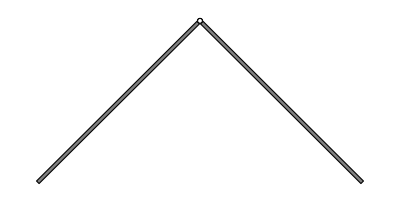

```mathematica
(* parameters for compass-gait walker *)
μ = 2;
β = 1;
L = 1+β;

a = 1/2;
g = 9.81/a;

NewBiped[]
SetGravity[g];
SetBipedHip[μ,0, 0];
AddBipedLeg[1,β,0,L];
CompileBiped[]
```

### Step 2) Generate gaits

Found 2 switching time(s).  About to search for gaits at these times.  To abort a search from the current switching time, use the notebook's Abort Evaluation command 'ALT+.'.  Don't worry about aborting, any gaits found will be saved.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0.624159}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 74.6657055 s to run and has 36 points.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0.68465}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 151.291485 s to run and has 36 points.

There are 2 walking branches found.

Branch: 1

switching time: 0.624159

# of gaits in this branch: 36

max normed error between post-impact states: 9.75046×10^-9

shortest gait time: 0.327073

longest gait time: 0.624159

steepest incline: 145.196°

min step size: 0.02

max step size: 0.946251

Branch: 2

switching time: 0.68465

# of gaits in this branch: 36

max normed error between post-impact states: 1.733×10^-8

shortest gait time: 0.68465

longest gait time: 1.67185

steepest incline: 55.9048°

min step size: 0.02

max step size: 0.870854

Singular Points:

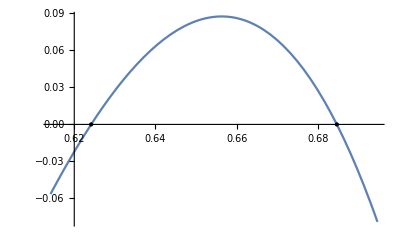

State-Time Plot:

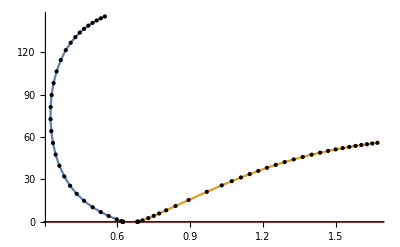

```mathematica
(* generating gaits takes about 285 s total to generate 35 points per curve. *)
FindGaits[0.5, 0.8, 35, 1/50];
GaitInfo[]
```

### Step 3) Animate gaits

```mathematica
(* a walking gait *)
AnimateGait[1,10]

(* an overhand brachiating gait *)
AnimateGait[1,-1]
```

### Useful tools

```mathematica
(* trouble finding a gait? plot the cost function. *)
PlotBipedDet[0.5, 0.8]

(* roots exist, but not finding roots in interval? use a fixed step size to search for them. *)
FindGaits[0, 1, 3, 1/50, "approxRoot"-> {StartingStepSize-> 1/1500, Method-> "ExplicitEuler"}];

(* just want the data?  get the trajectory. *)
SimulateGait[2, -1]
```

## Simplest Walking Model

-Graphics-

Based on the model above [1], but with M >> m instead of using dynamics in the limiting case where the ratio goes to zero.

[1] Garcia,M., A. Chatterjee, A. Ruina, and A. Coleman, "The Simplest Walking Model: Stability, Complexity, and Scaling", J. of Biomechanical Engineering, 120(2), 1998.

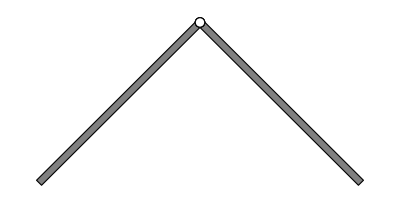

Found 2 switching time(s).  About to search for gaits at these times.  To abort a search from the current switching time, use the notebook's Abort Evaluation command 'ALT+.'.  Don't worry about aborting, any gaits found will be saved.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 3.12837}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 181.462302 s to run and has 36 points.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 3.80662}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 377.8737988 s to run and has 36 points.

There are 2 walking branches found.

Branch: 1

switching time: 3.12837

# of gaits in this branch: 36

max normed error between post-impact states: 1.21768×10^-8

shortest gait time: 2.19885

longest gait time: 3.12837

steepest incline: 92.9285°

min step size: 0.004

max step size: 0.166528

Branch: 2

switching time: 3.80662

# of gaits in this branch: 36

max normed error between post-impact states: 1.6724×10^-8

shortest gait time: 3.80662

longest gait time: 6.43934

steepest incline: 56.1898°

min step size: 0.004

max step size: 0.454883

Singular Points:

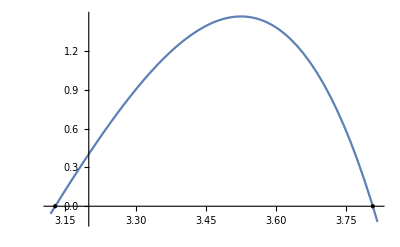

State-Time Plot:

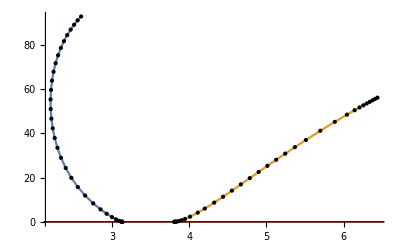

```mathematica
(* parameters *)
m = 1/100;
M = 1;
L = 1;

g = 1;

NewBiped[]
SetGravity[g];
SetBipedHip[1,0, 0];
AddBipedLeg[m/M,L,0,L];
CompileBiped[]

(* generating gaits takes about 602 s total to generate 35 points per curve. *)
FindGaits[0, 4, 35, 1/250];
GaitInfo[]

AnimateGait[1,12]
```

## Compass Gait Biped with Torso

-Graphics-

Based on the model above [1], but with no springs (K = 0).

[1] P. X. M. La Hera, A. S. Shiriaev, L. B. Freidovich, U. Mettin, and
S. V. Gusev, “Stable walking gaits for a three-link planar biped robot
with one actuator,” IEEE Transactions on Robotics, vol. 29, no. 3, pp.
589–601, Jun 2013.

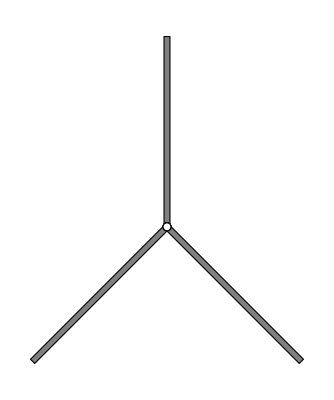

Found 2 switching time(s).  About to search for gaits at these times.  To abort a search from the current switching time, use the notebook's Abort Evaluation command 'ALT+.'.  Don't worry about aborting, any gaits found will be saved.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.661798}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 140.610952 s to run and has 36 points.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.668728}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 245.967895 s to run and has 36 points.

There are 2 walking branches found.

Branch: 1

switching time: 0.661798

# of gaits in this branch: 36

max normed error between post-impact states: 2.65143×10^-8

shortest gait time: 0.30775

longest gait time: 0.661798

steepest incline: 136.723°

min step size: 0.02

max step size: 0.726927

Branch: 2

switching time: 0.668728

# of gaits in this branch: 36

max normed error between post-impact states: 2.42747×10^-8

shortest gait time: 0.668728

longest gait time: 1.16311

steepest incline: 33.3002°

min step size: 0.02

max step size: 0.60786

Singular Points:

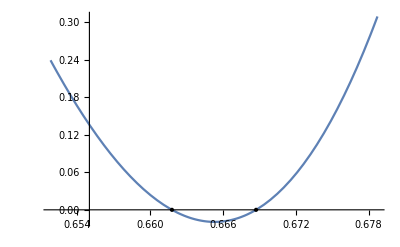

State-Time Plot:

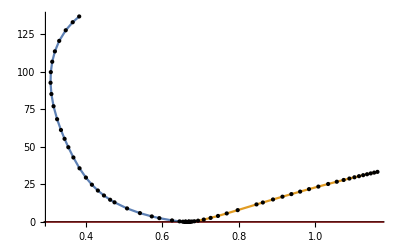

```mathematica
(* parameters *)
m = 5;
Mh = 15;
Mt = 15;
r = 1;
L = 1;

NewBiped[];
(* by default the value of gravity is 9.81. *)
SetBipedHip[Mh,0, 0];
AddBipedLeg[m,r/2,0,r];
AddBipedTorso[Mt,L,0,L];
CompileBiped[]

(* generating gaits takes about 414 s total to generate 35 points per curve. *)
FindGaits[0, 1, 35, 1/50];
GaitInfo[]

AnimateGait[1,18]
```

## RABBIT

-Graphics-

Based on the model above [1].

[1] E. R. Westervelt, J. W. Grizzle, and D. E. Koditschek, “Hybrid Zero Dynamics of Planar Biped Walkers,” IEEE Transactions on Automatic Control, vol. 48, no. 1, pp. 42–56, Jan. 2003.

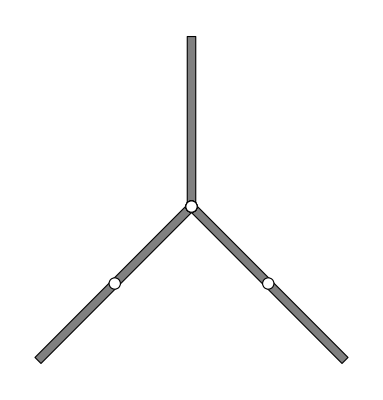

Found 2 switching time(s).  About to search for gaits at these times.  To abort a search from the current switching time, use the notebook's Abort Evaluation command 'ALT+.'.  Don't worry about aborting, any gaits found will be saved.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.679752}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 177.802 s to run and has 36 points.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1.27038}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 271.119454 s to run and has 36 points.

There are 2 walking branches found.

Branch: 1

switching time: 0.679752

# of gaits in this branch: 36

max normed error between post-impact states: 9.17791×10^-10

shortest gait time: 0.679752

longest gait time: 0.685675

steepest incline: 179.992°

min step size: 0.02

max step size: 0.216242

Branch: 2

switching time: 1.27038

# of gaits in this branch: 36

max normed error between post-impact states: 1.3013×10^-10

shortest gait time: 1.27038

longest gait time: 1.27041

steepest incline: 180.°

min step size: 0.00115717

max step size: 0.02

Singular Points:

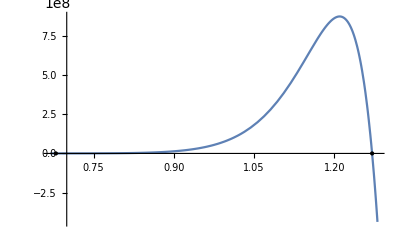

State-Time Plot:

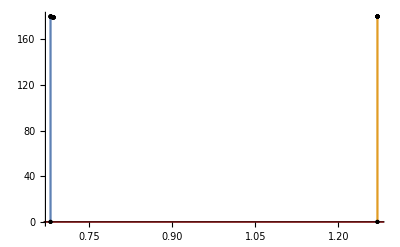

```mathematica
(* parameters *)
Mtor = 20;
Mfem = 6.8;
Mtib = 3.2;

Ltor = 0.625;
Lfem = 0.4;
Ltib = 0.4;

Itor = 2.22;
Ifem = 1.08;
Itib = 0.93;

ptor = 0.2;
pfem = 0.163;
ptib = 0.128;

NewBiped[];
(* by default the value of gravity is 9.81. *)
SetBipedHip[0,0, 0];
AddBipedLeg[Mfem,pfem,Ifem,Lfem];
AddBipedLeg[Mtib,ptib,Itib,Ltib];
AddBipedTorso[Mtor,ptor,Itor,Ltor];
CompileBiped[]

(* generating gaits takes about 414 s total to generate 35 points per curve. *)
FindGaits[0, 1.3, 35, 1/50];
GaitInfo[]

AnimateGait[1,-1]
```

## Anthropomorphic Biped

-Graphics-
Based on the human body data from [1], but coordinate system pictured above has been modified to accomodate the restrictions placed on this package.

[1] R. Dumas, L. Cheze, and J.P. Verriest, “Adjustment to McConville et al. and Young et al. body segment inertial parameters,” Journal of Biomechanics, vol. 40, no. 3, pp.  543-553, 2007.

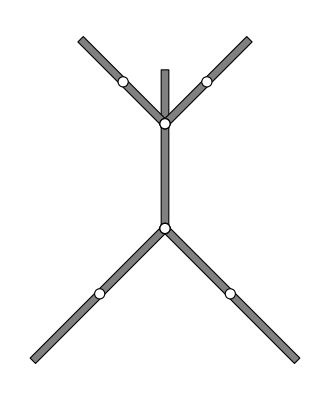

```mathematica
(* segment lengths (meters) *)
head = 221/1000;
torso = 429/1000;
arm = 243/1000;
forearm = 247/1000;
pelvis = 107/1000;
thigh = 379/1000;
leg = 388/1000;

(* total masses (kilograms) *)
mass = 63.9;
(* total masses (meters) *)
length = 1.61;

NewBiped[];
(* head *)
m = 6.7/100 mass;
AddBipedHead[m, head 59.7/100, (head 34/100)^2 * m, 221/1000];
(* torso *)
m = 30.4/100 mass;
AddBipedTorso[m, torso (1-43.6/100), (torso 29/100)^2 * m, 429/1000];
(* arms *)
m = 2.2/100 mass;
AddBipedArm[m, arm 45.5/100, (arm 33/100)^2 * m, 243/1000];
(* forearms *)
m = 1.3/100 mass;
AddBipedArm[m, forearm 41.1/100, (forearm 25/100)^2 * m, 247/1000];
(* pelvis *)
m = 14.6/100 mass;
SetBipedHip[m, pelvis (1-23.2/100), (pelvis 79/100)^2 * m];
(* thighs *)
m = 14.6/100 mass;
AddBipedLeg[m, thigh 37.7/100, (thigh 32/100)^2 * m, 379/1000];
(* legs *)
m = 4.5/100 mass;
AddBipedLeg[m, leg 40.4/100, (leg 28/100)^2 * m, 388/1000];
CompileBiped[]
```

Found 1 switching time(s).  About to search for gaits at these times.  To abort a search from the current switching time, use the notebook's Abort Evaluation command 'ALT+.'.  Don't worry about aborting, any gaits found will be saved.

nlc0::bifurcation: Bifurcation at {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0.281436}.  Selecting tangent 1.

nlcurve::info: "biped gait" took 4502.2250882 s to run and has 701 points.

There are 1 walking branches found.

Branch: 1

switching time: 0.281436

# of gaits in this branch: 701

max normed error between post-impact states: 8.56512×10^-7

shortest gait time: 0.211745

longest gait time: 0.301281

steepest incline: 179.997°

min step size: 0.02

max step size: 0.02

Singular Points:

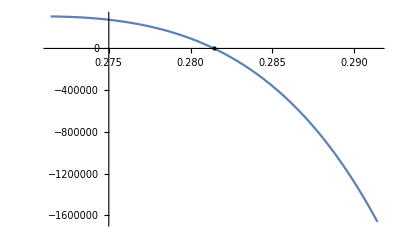

State-Time Plot:

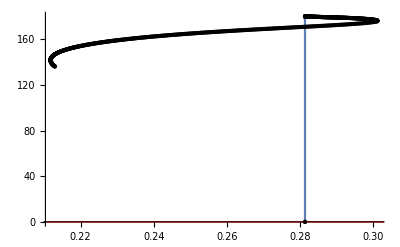

```mathematica
(* really slow at tighter tolerances so tweak various subfunctions. *)

(* generating gaits takes about 4573 s total to generate 700 points per curve. *)

FindGaits[0.228, 0.3, 700, 1/50, "map"-> {AccuracyGoal-> 8, PrecisionGoal-> 8, 
Compiled-> False, MaxSteps-> Infinity}, "nlc0"-> {Tolerance-> 10^-9}, Constant-> True];

GaitInfo[]
```

```mathematica
AnimateGait[1, -1]
```